## Setup: Functions to determine hom. steady states and dispersion relations

Run entire setup cell group below. Then test with the usage example.

### Setup

#### Variables and reaction kinetics

```mathematica
memVars={md,mde};
cytVars={cD,cDD,cE};
```

```mathematica
memReact={
(kD+kdD md)(cD-cDD)-kdE md cE,
kdE md cE-kde mde
};
cytCouple={
-(kD+kdD md)(cD-cDD)+kde mde,
kde mde,
kde mde-kdE md cE
};
```

Symmetric mode bulk-boundary coupling coefficient

```mathematica
Γs[q_,α_,h_]:=Sqrt[α+q^2]Tanh[Sqrt[α+q^2]h]
```

#### Reactive equilibria

```mathematica
nSolveHomEq[params_]:=SortBy[Cases[
Chop@NSolve[
Join[memReact,
{
cytCouple[[1]],cytCouple[[3]],
DD Γs[0,λ/DD,h] cDD-cytCouple[[2]],
h cD+(md+mde)-h nD,
h cE+mde-h nE
}
]/.params,
Join[memVars,cytVars]
],
{HoldPattern[_->(_?(Im@#==0&&#≥0&))]..}
],
First
]
```

#### Linear stability

```mathematica
boxJacobianSym=ArrayFlatten[{
{
D[memReact,{memVars}]-q^2 DiagonalMatrix[{Dd,Dde}]-σ IdentityMatrix[Length@memVars],
D[memReact,{cytVars}]
},
{
D[cytCouple,{memVars}],
D[cytCouple,{cytVars}]-DiagonalMatrix[{
DD Γs[q,σ/DD,h],DD Γs[q,(σ+λ)/DD,h],DE Γs[q,σ/DE,h]
}]
}
}];
```

```mathematica
boxJacobianASym=boxJacobianSym/.Tanh->Coth;
```

```mathematica
sampleDetRoot[det_,initList_]:=
First@MaximalBy[Quiet@Check[σ/.FindRoot[det,{σ,#}],-100-I]&/@initList,Re]
```

```mathematica
findDispRelSym[params_,eq_,qMax_,qRes_:100]:=With[{
detParams=Det[boxJacobianSym/.eq/.params]
},
Table[
{qIter,sampleDetRoot[detParams/.q->qIter,{0.1,0.1+0.1I,0.5,0.5+I,1.,1.+I,5.,5.+I,10.,10.+I,20.}]},
{qIter,0,qMax,qMax/qRes}
]
]
```

```mathematica
findDispRelASym[params_,eq_,qMax_,qRes_:100]:=With[{
detParams=Det[boxJacobianASym/.eq/.params]
},
Table[
{qIter,sampleDetRoot[detParams/.q->qIter,{0.1,0.1+0.1I,0.5,0.5+I,1.,1.+I,5.,5.+I,10.,10.+I,20.}]},
{qIter,0,qMax,qMax/qRes}
]
]
```

### Usage example

```mathematica
testParams={
nD->400,nE->300,
DD->60,DE->60,Dd->0.013,Dde->0.013,
λ->6,
kD->0.1,kdD->0.1,kdE->0.15,kde->0.5,
h->5
};
```

```mathematica
testEq=Last@nSolveHomEq[testParams]
```

{md→252.291,mde→1407.05,cD→68.1321,cDD→40.3568,cE→18.5903}

```mathematica
dispRelSym=findDispRelSym[testParams,testEq,1.0 (* max q *)];
dispRelASym=findDispRelASym[testParams,testEq,1.0 (* max q *)];
```

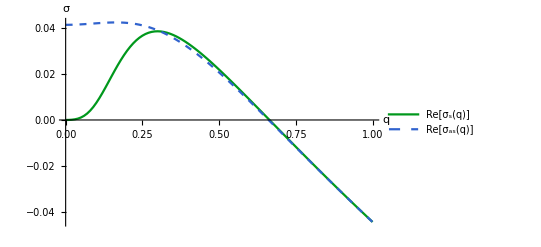

```mathematica
ListPlot[{Re@dispRelSym,Re@dispRelASym},
Joined->True,
PlotLegends->{"Re[σ_s(q)]","Re[σ_as(q)]"},
PlotStyle->{ColorData[112,"ColorList"][[4]],Directive[Dashed,ColorData[112,"ColorList"][[2]]]},
AxesLabel->{q,σ}
]
```

## Example dispersion relations

```mathematica
fixedParams={
nD->400,
DD->60,DE->60,Dd->0.013,Dde->0.013,
λ->6,
kD->0.1,kdD->0.1,kdE->0.15,kde->0.5
};
```

```mathematica
plotDispRels[params_,maxq_]:=ListPlot[{Re@findDispRelSym[params,#,maxq],Re@findDispRelASym[params,#,maxq]}&@
Last@nSolveHomEq[params],
Joined->True,
PlotLegends->{"Re[σ_s(q)]","Re[σ_as(q)]"},
PlotStyle->{ColorData[112,"ColorList"][[4]],Directive[Dashed,ColorData[112,"ColorList"][[2]]]},
AxesLabel->{q,σ}
]
```

#### Only symmetric mode instability (n_E=315,H=2 2)

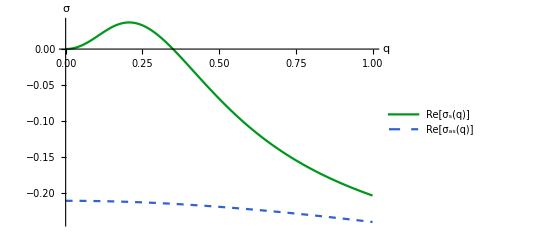

```mathematica
plotDispRels[Join[{nE->320,h->1},fixedParams],1.0]
```

#### Local anti-symmetric mode instability + lateral symmetric instability (n_E=280,H=2 7)

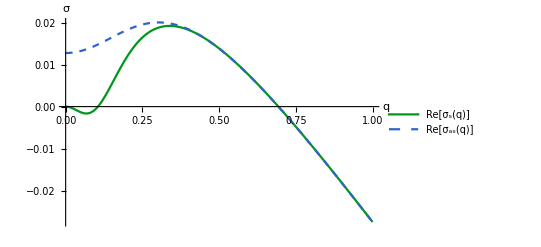

```mathematica
plotDispRels[Join[{nE->280,h->7},fixedParams],1.0]
```

#### Only local anti-symmetric mode instability (n_E=270,H=2 5)

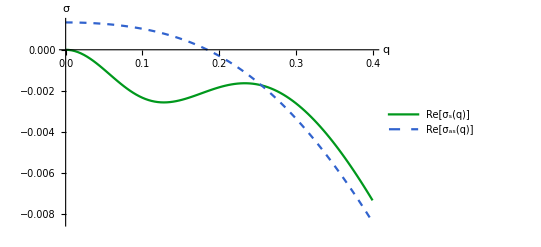

```mathematica
plotDispRels[Join[{nE->270,h->5},fixedParams],0.4]
```

#### Large bulk height: incommensurable lateral instability, no local instability (n_E=220,H=2 20)

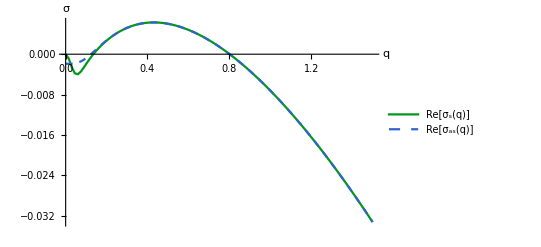

```mathematica
plotDispRels[Join[{nE->220,h->20},fixedParams],1.5]
```

#### Large bulk height: commensurable lateral instability, no local instability (n_E=250,H=2 20)

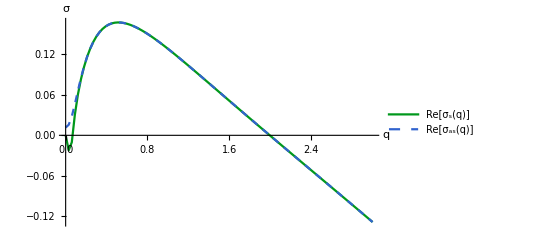

```mathematica
plotDispRels[Join[{nE->250,h->20},fixedParams],3]
```

#### Large bulk height: commensurable lateral instability, local instability (n_E=270,H=2 20)

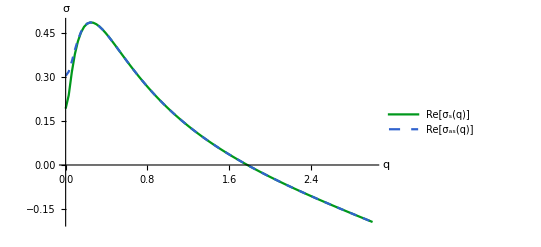

```mathematica
plotDispRels[Join[{nE->260,h->20},fixedParams],3]
```

## Setup: Tools for dispersion relation classification

```mathematica
findSignChangePos[list_]:=Position[Times@@#&/@Partition[Sign[Re@list],2,1],-1|0];
```

```mathematica
interpolateRealRoots[list_]:=With[{
signChangePos=findSignChangePos@list[[All,2]]
},
Table[
With[{x0=#[[1,1]]-#[[1,2]](#[[2,1]]-#[[1,1]])/(#[[2,2]]-#[[1,2]])&@Re@list[[{p[[1]],p[[1]]+1}]]},
{
x0,
Chop[#[[1,2]]+(#[[2,2]]-#[[1,2]])/(#[[2,1]]-#[[1,1]])(x0-#[[1,1]])&@list[[{p[[1]],p[[1]]+1}]]],
Sign[#[[2,2]]-#[[1,2]]&@Re@list[[{p[[1]],p[[1]]+1}]]],
{p[[1]],p[[1]]+1}
}
],
{p,signChangePos}
]
]
```

```mathematica
interpolateRealExtrema[list_]:=With[{
finiteDifferenceRoots=interpolateRealRoots[
Transpose[{
Mean/@Partition[list[[All,1]],2,1],
Differences[Re@list[[All,2]]]/Differences[list[[All,1]]]
}]
]
},
Table[{
root[[1]],
First@MaximalBy[list[[root[[-1]],2]],Abs@Re@#&],
root[[3]],
root[[4]]
},
{root,finiteDifferenceRoots}
]
]
```

```mathematica
getKeyModes[dispRel_]:={
(* roots *)
interpolateRealRoots[Rest@dispRel][[All,{1,2}]],
(* maxima *)
DeleteDuplicates@Select[interpolateRealExtrema[dispRel],#[[3]]==-1&][[All,{1,2}]]
}
```

## (n_E,H)-parameter plane

```mathematica
fixedParams={
nD->400,
DD->60,DE->60,Dd->0.013,Dde->0.013,
λ->6,
kD->0.1,kdD->0.1,kdE->0.15,kde->0.5
};
```

### Loading precomputed steady states and dispersion relations

```mathematica
dispRelTableEH=Get[NotebookDirectory[]<>"disp-rel-table_nE=150-350-2_h=0.5-30-0.5.txt"];
```

```mathematica
numEqsTableEH=Map[Length@#[[2]]&,dispRelTableEH,{2}];
```

```mathematica
keyModeTableEH=Map[{#[[1]],getKeyModes[#[[3]]],getKeyModes[#[[4]]]}&,dispRelTableEH,{2}];
```

```mathematica
dataRangeEH={{150,350},{0.5,30}};
```

### Computation of steady states and dispersion relations

At the pre-set sampling resolution (100 steps in n_E, 60 steps in h) the computation takes about 1 h on a recent notebook CPU (single core run).

#### Laterally homogeneous steady states (reactive equilibria)

```mathematica
homEqsTableEH=Table[
{
{nEIter,hIter},
nSolveHomEq[Join[{nE->nEIter,h->hIter},fixedParams]][[All,All,2]]
},
{nEIter,150,350,2},{hIter,0.5,30,0.5}
];
```

```mathematica
dataRangeEH={{150,350},{0.5,30}};
```

```mathematica
numEqsTableEH=Map[Length@#[[2]]&,homEqsTableEH,{2}];
```

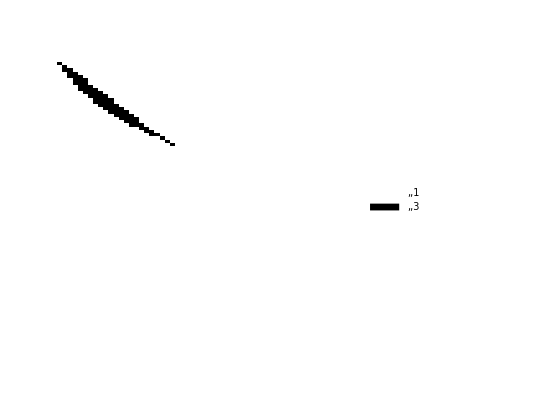

```mathematica
ArrayPlot[
Reverse@numEqsTableEH,
PlotLegends->Automatic,
DataRange->Reverse@dataRangeEH,
AspectRatio->1,
FrameTicks->Automatic,
ColorRules->{3->Black,1->White}
]
```

#### LSA (finding the dispersion relations)

```mathematica
dispRelTableEH=Map[Join[
#,
{
findDispRelSym[
Join[Thread[{nE,h}->#[[1]]],fixedParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
3,30
],
findDispRelASym[
Join[Thread[{nE,h}->#[[1]]],fixedParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
3,30
]
}
]&,
homEqsTableEH,{2}
];//AbsoluteTiming
```

{4442.95,Null}

```mathematica
keyModeTableEH=Map[{#[[1]],getKeyModes[#[[3]]],getKeyModes[#[[4]]]}&,dispRelTableEH,{2}];
```

### Plotting

Requires the dispersion relation data either loaded from a precomputed file or computed using the code in the previous section.

```mathematica
frameSettings={AspectRatio->1,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameTicks->{Automatic,Automatic},
FrameLabel->{"Total MinE density (n_(<E>))","Half bulk height (h = H/2)",None,None},
DataRange->Reverse@dataRangeEH,PlotRange->{{0,30},{150,350}}};
```

#### Lateral instability (vertically sym. mode)

```mathematica
hasLateralInstabilityTableEH=Map[If[Max@Re@#[[3,2;;-1,2]]>0,1,0]&,dispRelTableEH,{2}];
```

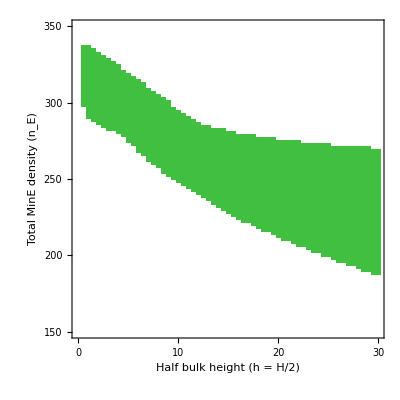

```mathematica
ArrayPlot[
Reverse@hasLateralInstabilityTableEH,
ColorRules->{0->White,1->RGBColor[0.25,0.75,0.25]},
Sequence@@frameSettings
]
```

#### Local instability (vertically anti-sym. mode)

```mathematica
hasASymLocalInstabilityTableEH=Map[If[Re@#[[4,1,2]]>0,1,0]&,dispRelTableEH,{2}];
```

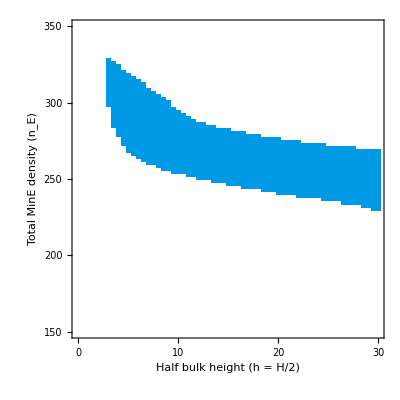

```mathematica
ArrayPlot[
Reverse[hasASymLocalInstabilityTableEH],
ColorRules->{0->White,1->RGBColor[0,0.6,0.9]},
Sequence@@frameSettings
]
```

#### Local instability (vertically sym. mode)

```mathematica
hasSymLocalInstabilityTableEH=Map[If[Chop[Re@#[[3,1,2]],10^-6]>0,1,0]&,dispRelTableEH,{2}];
```

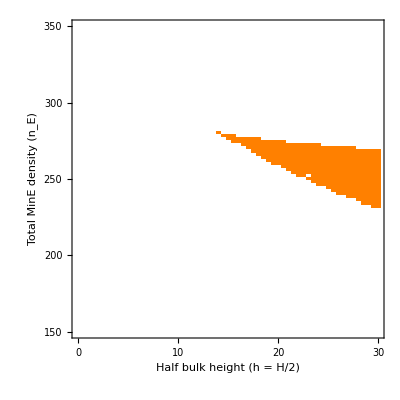

```mathematica
ArrayPlot[
Reverse[hasSymLocalInstabilityTableEH],
ColorRules->{0->White,1->RGBColor[1,0.5,0]},
Sequence@@frameSettings
]
```

#### Overlay

```mathematica
rasterRange={{0.5,150},{30,350}};
```

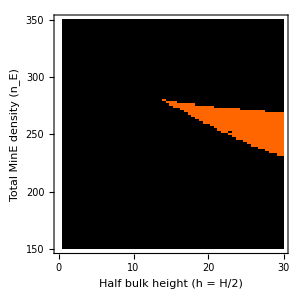

```mathematica
Graphics[{
Raster[numEqsTableEH/.{3->{0,0,0,0.8},1->{0,0,0,0}},rasterRange],
Raster[hasLateralInstabilityTableEH/.{1->{0.1,0.9,0.1,0.5},0->{0,0,0,0}},rasterRange],
Raster[hasASymLocalInstabilityTableEH/.{1->{0,0.5,1,0.5},0->{0,0,0,0}},rasterRange],
Raster[hasSymLocalInstabilityTableEH/.{1->{1,0.4,0,0.5},0->{0,0,0,0}},rasterRange]
},
Background->White,
PlotRange->{{0,30},{150,350}},
AspectRatio->1,Frame->True,FrameStyle->Directive[Black,FontSize->14],
FrameTicks->{Range[0,30,10],Range[150,350,50],None,None},
FrameLabel->{"Half bulk height (h = H/2)","Total MinE density (n_(<E>))",None,None}
]
```

## (n_D,n_E/n_D)-parameter plane

```mathematica
nDRange=Range[0,800,10];
ratioRange=Range[0.3,1,0.01];
```

At the pre-set sampling resolution (50x50 grid in (n_E,n_D)-parameter plane) the computation for each bulk height requires about 1 h on a recent notebook CPU (single core run).

```mathematica
frameSettings={
AspectRatio->1,
Frame->True,FrameStyle->Black,
FrameLabel->{"n_E/n_D","n_D"},
DataRange->{MinMax@nDRange,MinMax@ratioRange},PlotRange->{MinMax@nDRange,MinMax@ratioRange},
FrameTicks->{
{#,#,{0,0.015}}&/@{0.4,0.6,0.8,1},
{#,#,{0,0.015}}&/@{0,400,800}
}
};
```

### h=1 µm

```mathematica
fixedParams={
DD->60,DE->60,Dd->0.013,Dde->0.013,
λ->6,
kD->0.1,kdD->0.1,kdE->0.15,kde->0.5,
h->1
};
```

#### Laterally homogeneous steady states (reactive equilibria)

```mathematica
homEqsTableDE[h->1]=Table[
{
{nDIter,nEIter},
nSolveHomEq[Join[{nE->nEIter,nD->nDIter},fixedParams]][[All,All,2]]
},
{nEIter,nDIter ratioRange},{nDIter,nDRange}
];//AbsoluteTiming
```

{88.3211,Null}

```mathematica
numEqsTableDE[h->1]=Map[Length@#[[2]]&,homEqsTableDE[h->1],{2}];
```

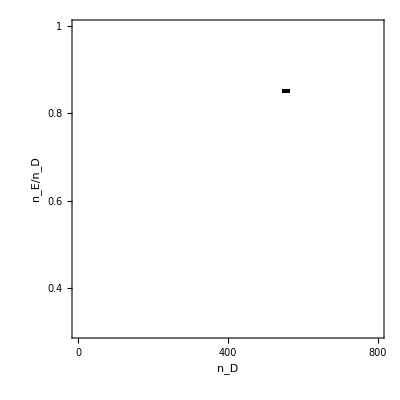

```mathematica
ArrayPlot[
Reverse@numEqsTableDE[h->1],
ColorRules->{3->Black,1->White},
Sequence@@frameSettings
]
```

#### LSA (finding the dispersion relations)

```mathematica
dispRelTableDE[h->1]=Map[Join[
#,
{
findDispRelSym[
Join[Thread[{nD,nE}->#[[1]]],fixedParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
3,30
],
findDispRelASym[
Join[Thread[{nD,nE}->#[[1]]],fixedParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
3,30
]
}
]&,
homEqsTableDE[h->1],{2}
];//AbsoluteTiming
```

{6095.15,Null}

```mathematica
Put[dispRelTableDE[h->1],NotebookDirectory[]<>"disp-rel-table_h=1_nD=0-800-10_EDratio=0.3-1-0.01.txt"];
```

```mathematica
keyModeTableDE[h->1]=Map[{#[[1]],getKeyModes[#[[3]]],getKeyModes[#[[4]]]}&,dispRelTableDE[h->1],{2}];
```

#### Lateral instability (vertically sym. mode)

```mathematica
hasLateralInstabilityTableDE[h->1]=Map[If[Max@Re@#[[3,2;;-1,2]]>0,1,0]&,dispRelTableDE[h->1],{2}];
```

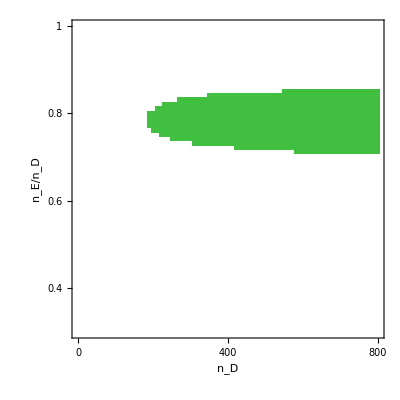

```mathematica
ArrayPlot[
Reverse@hasLateralInstabilityTableDE[h->1],
ColorRules->{0->White,1->RGBColor[0.25,0.75,0.25]},
Sequence@@frameSettings
]
```

#### Local instability (vertically anti-sym. mode)

```mathematica
hasASymLocalInstabilityTableDE[h->1]=Map[If[Re@#[[4,1,2]]>10^-6,1,0]&,dispRelTableDE[h->1],{2}];
```

```mathematica
ArrayPlot[
Reverse@hasASymLocalInstabilityTableDE[h->1],
ColorRules->{0->White,1->RGBColor[0,0.6,0.9]},
Sequence@@frameSettings
]
```

-Graphics-

#### Local instability (vertically sym. mode)

```mathematica
hasSymLocalInstabilityTableDE[h->1]=Map[If[Chop[Re@#[[3,1,2]],10^-6]>0,1,0]&,dispRelTableDE[h->1],{2}];
```

```mathematica
ArrayPlot[
Reverse@hasSymLocalInstabilityTableDE[h->1],
ColorRules->{0->White,1->RGBColor[1,0.5,0]},
Sequence@@frameSettings
]
```

-Graphics-

### h=5 µm

```mathematica
fixedParams={
DD->60,DE->60,Dd->0.013,Dde->0.013,
λ->6,
kD->0.1,kdD->0.1,kdE->0.15,kde->0.5,
h->5
};
```

#### Laterally homogeneous steady states (reactive equilibria)

```mathematica
homEqsTableDE[h->5]=Table[
{
{nDIter,nEIter},
nSolveHomEq[Join[{nE->nEIter,nD->nDIter},fixedParams]][[All,All,2]]
},
{nEIter,nDIter ratioRange},{nDIter,nDRange}
];//AbsoluteTiming
```

{90.4487,Null}

```mathematica
numEqsTableDE[h->5]=Map[Length@#[[2]]&,homEqsTableDE[h->5],{2}];
```

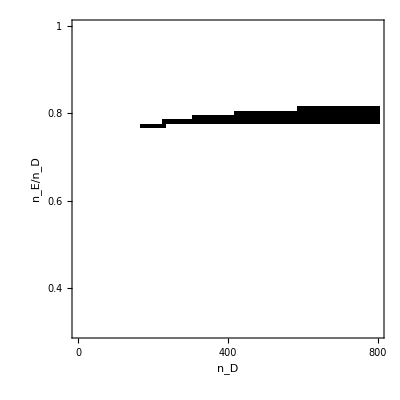

```mathematica
ArrayPlot[
Reverse@numEqsTableDE[h->5],
ColorRules->{3->Black,1->White},
Sequence@@frameSettings
]
```

#### LSA (finding the dispersion relations)

```mathematica
dispRelTableDE[h->5]=Map[Join[
#,
{
findDispRelSym[
Join[Thread[{nD,nE}->#[[1]]],fixedParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
3,30
],
findDispRelASym[
Join[Thread[{nD,nE}->#[[1]]],fixedParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
3,30
]
}
]&,
homEqsTableDE[h->5],{2}
];//AbsoluteTiming
```

{6765.61,Null}

```mathematica
Put[dispRelTableDE[h->5],NotebookDirectory[]<>"disp-rel-table_h=5_nD=0-800-10_EDratio=0.3-1-0.01.txt"];
```

```mathematica
keyModeTableDE[h->5]=Map[{#[[1]],getKeyModes[#[[3]]],getKeyModes[#[[4]]]}&,dispRelTableDE[h->5],{2}];
```

#### Lateral instability (vertically sym. mode)

```mathematica
hasLateralInstabilityTableDE[h->5]=Map[If[Max@Re@#[[3,2;;-1,2]]>0,1,0]&,dispRelTableDE[h->5],{2}];
```

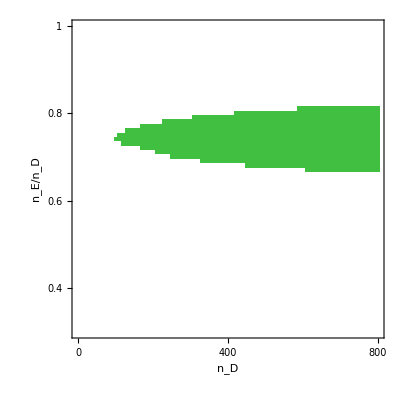

```mathematica
ArrayPlot[
Reverse@hasLateralInstabilityTableDE[h->5],
ColorRules->{0->White,1->RGBColor[0.25,0.75,0.25]},
Sequence@@frameSettings
]
```

#### Local instability (vertically anti-sym. mode)

```mathematica
hasASymLocalInstabilityTableDE[h->5]=Map[If[Re@#[[4,1,2]]>10^-6,1,0]&,dispRelTableDE[h->5],{2}];
```

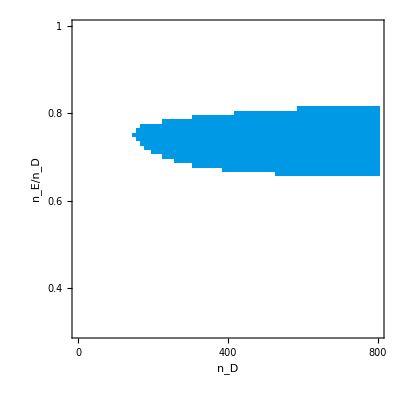

```mathematica
ArrayPlot[
Reverse@hasASymLocalInstabilityTableDE[h->5],
ColorRules->{0->White,1->RGBColor[0,0.6,0.9]},
Sequence@@frameSettings
]
```

#### Local instability (vertically sym. mode)

```mathematica
hasSymLocalInstabilityTableDE[h->5]=Map[If[Chop[Re@#[[3,1,2]],10^-6]>0,1,0]&,dispRelTableDE[h->5],{2}];
```

```mathematica
ArrayPlot[
Reverse@hasSymLocalInstabilityTableDE[h->5],
ColorRules->{0->White,1->RGBColor[1,0.5,0]},
Sequence@@frameSettings
]
```

-Graphics-

### h=20 µm

```mathematica
fixedParams={
DD->60,DE->60,Dd->0.013,Dde->0.013,
λ->6,
kD->0.1,kdD->0.1,kdE->0.15,kde->0.5,
h->20
};
```

#### Laterally homogeneous steady states (reactive equilibria)

```mathematica
homEqsTableDE[h->20]=Table[
{
{nDIter,nEIter},
nSolveHomEq[Join[{nE->nEIter,nD->nDIter},fixedParams]][[All,All,2]]
},
{nEIter,nDIter ratioRange},{nDIter,nDRange}
];//AbsoluteTiming
```

{90.0328,Null}

```mathematica
numEqsTableDE[h->20]=Map[Length@#[[2]]&,homEqsTableDE[h->20],{2}];
```

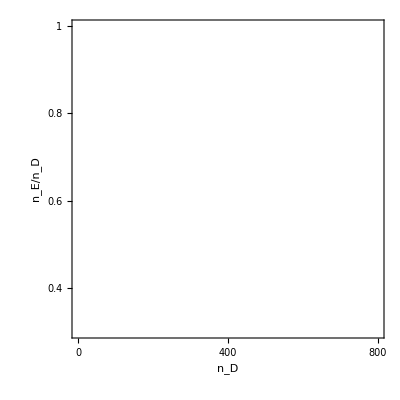

```mathematica
ArrayPlot[
Reverse@Transpose@numEqsTableDE[h->20],
ColorRules->{3->Black,1->White},
Sequence@@frameSettings
]
```

#### LSA (finding the dispersion relations)

```mathematica
dispRelTableDE[h->20]=Map[Join[
#,
{
findDispRelSym[
Join[Thread[{nD,nE}->#[[1]]],fixedParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
3,30
],
findDispRelASym[
Join[Thread[{nD,nE}->#[[1]]],fixedParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
3,30
]
}
]&,
homEqsTableDE[h->20],{2}
];//AbsoluteTiming
```

{6571.5,Null}

```mathematica
Put[dispRelTableDE[h->20],NotebookDirectory[]<>"disp-rel-table_h=20_nD=0-800-10_EDratio=0.3-1-0.01.txt"];
```

```mathematica
keyModeTableDE[h->20]=Map[{#[[1]],getKeyModes[#[[3]]],getKeyModes[#[[4]]]}&,dispRelTableDE[h->20],{2}];
```

#### Lateral instability (vertically sym. mode)

```mathematica
hasLateralInstabilityTableDE[h->20]=Map[If[Max@Re@#[[3,2;;-1,2]]>0,1,0]&,dispRelTableDE[h->20],{2}];
```

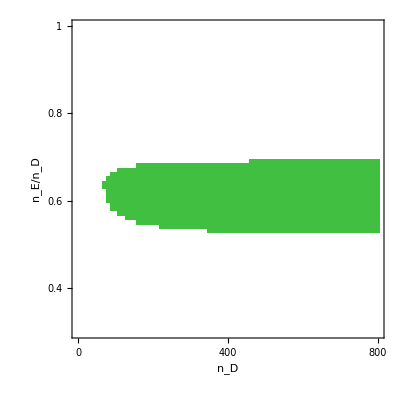

```mathematica
ArrayPlot[
Reverse@hasLateralInstabilityTableDE[h->20],
ColorRules->{0->White,1->RGBColor[0.25,0.75,0.25]},
Sequence@@frameSettings
]
```

#### Local instability (vertically anti-sym. mode)

```mathematica
hasASymLocalInstabilityTableDE[h->20]=Map[If[Re@#[[4,1,2]]>10^-6,1,0]&,dispRelTableDE[h->20],{2}];
```

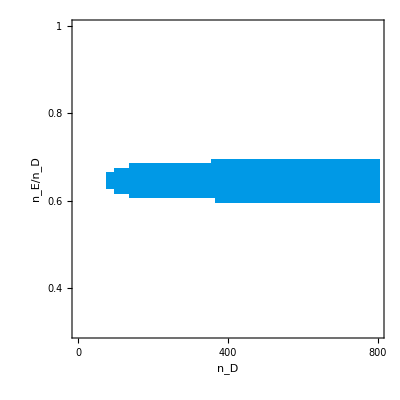

```mathematica
ArrayPlot[
Reverse@hasASymLocalInstabilityTableDE[h->20],
ColorRules->{0->White,1->RGBColor[0,0.6,0.9]},
Sequence@@frameSettings
]
```

#### Local instability (vertically sym. mode)

```mathematica
hasSymLocalInstabilityTableDE[h->20]=Map[If[Chop[Re@#[[3,1,2]],10^-6]>0,1,0]&,dispRelTableDE[h->20],{2}];
```

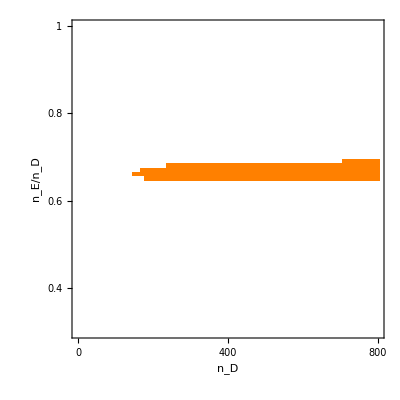

```mathematica
ArrayPlot[
Reverse@hasSymLocalInstabilityTableDE[h->20],
ColorRules->{0->White,1->RGBColor[1,0.5,0]},
Sequence@@frameSettings
]
```

### h=40 µm

```mathematica
fixedParams={
DD->60,DE->60,Dd->0.013,Dde->0.013,
λ->6,
kD->0.1,kdD->0.1,kdE->0.15,kde->0.5,
h->40
};
```

#### Laterally homogeneous steady states (reactive equilibria)

```mathematica
homEqsTableDE[h->40]=Table[
{
{nDIter,nEIter},
nSolveHomEq[Join[{nE->nEIter,nD->nDIter},fixedParams]][[All,All,2]]
},
{nEIter,nDIter ratioRange},{nDIter,nDRange}
];//AbsoluteTiming
```

{89.6858,Null}

```mathematica
numEqsTableDE[h->40]=Map[Length@#[[2]]&,homEqsTableDE[h->40],{2}];
```

```mathematica
ArrayPlot[
Reverse@Transpose@numEqsTableDE[h->40],
ColorRules->{3->Black,1->White},
Sequence@@frameSettings
]
```

-Graphics-

#### LSA (finding the dispersion relations)

```mathematica
dispRelTableDE[h->40]=Map[Join[
#,
{
findDispRelSym[
Join[Thread[{nD,nE}->#[[1]]],fixedParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
3,30
],
findDispRelASym[
Join[Thread[{nD,nE}->#[[1]]],fixedParams],
Thread[Join[memVars,cytVars]->#[[2,-1]]],
3,30
]
}
]&,
homEqsTableDE[h->40],{2}
];//AbsoluteTiming
```

{6492.14,Null}

```mathematica
Put[dispRelTableDE[h->40],NotebookDirectory[]<>"disp-rel-table_h=40_nD=0-800-10_EDratio=0.3-1-0.01.txt"];
```

```mathematica
keyModeTableDE[h->40]=Map[{#[[1]],getKeyModes[#[[3]]],getKeyModes[#[[4]]]}&,dispRelTableDE[h->40],{2}];
```

#### Lateral instability (vertically sym. mode)

```mathematica
hasLateralInstabilityTableDE[h->40]=Map[If[Max@Re@#[[3,2;;-1,2]]>0,1,0]&,dispRelTableDE[h->40],{2}];
```

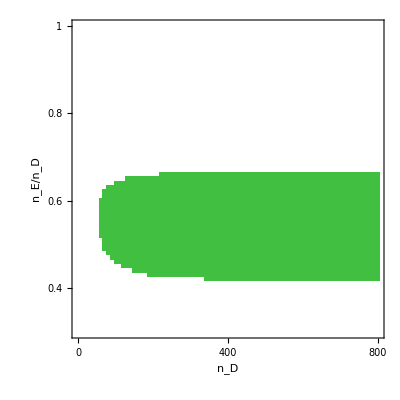

```mathematica
ArrayPlot[
Reverse@hasLateralInstabilityTableDE[h->40],
ColorRules->{0->White,1->RGBColor[0.25,0.75,0.25]},
Sequence@@frameSettings
]
```

#### Local instability (vertically anti-sym. mode)

```mathematica
hasASymLocalInstabilityTableDE[h->40]=Map[If[Re@#[[4,1,2]]>10^-6,1,0]&,dispRelTableDE[h->40],{2}];
```

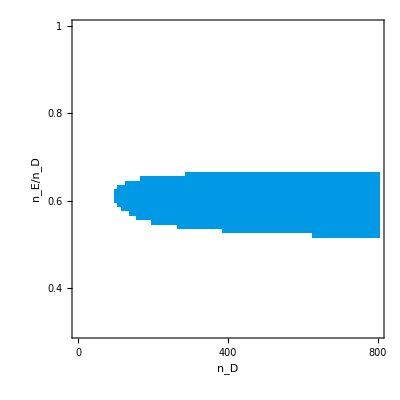

```mathematica
ArrayPlot[
Reverse@hasASymLocalInstabilityTableDE[h->40],
ColorRules->{0->White,1->RGBColor[0,0.6,0.9]},
Sequence@@frameSettings
]
```

#### Local instability (vertically sym. mode)

```mathematica
hasSymLocalInstabilityTableDE[h->40]=Map[If[Chop[Re@#[[3,1,2]],10^-6]>0,1,0]&,dispRelTableDE[h->40],{2}];
```

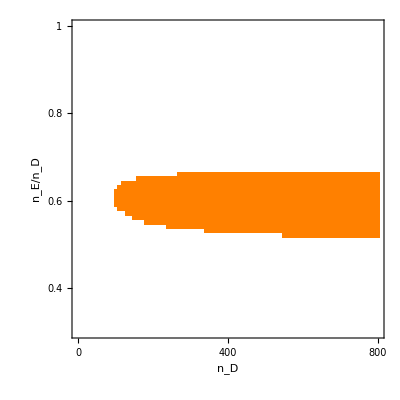

```mathematica
ArrayPlot[
Reverse@hasSymLocalInstabilityTableDE[h->40],
ColorRules->{0->White,1->RGBColor[1,0.5,0]},
Sequence@@frameSettings
]
```

### Overlay plots

```mathematica
rasterRange={{0,0.3},{800,1}};
```

```mathematica
Row[
Graphics[{
Raster[numEqsTableDE[h->#]/.{3->{0,0,0,0.7},1->{0,0,0,0}},rasterRange],
Raster[hasLateralInstabilityTableDE[h->#]/.{1->{0.1,0.9,0.1,0.5},0->{0,0,0,0}},rasterRange],
Raster[hasASymLocalInstabilityTableDE[h->#]/.{1->{0,0.5,1,0.5},0->{0,0,0,0}},rasterRange],
Raster[hasSymLocalInstabilityTableDE[h->#]/.{1->{1,0.4,0,0.5},0->{0,0,0,0}},rasterRange]
},
Background->White,
PlotRangePadding->None,
AspectRatio->1.5,
Frame->True,FrameStyle->Directive[Black,FontSize->14],
FrameLabel->{"n_D","n_E/n_D",Style["H = "<>ToString[2#],FontSize->16]},
FrameTicks->{
{#,#,{0,0.015}}&/@{0,400,800},
{#,#,{0,0.015}}&/@{0.4,0.6,0.8,1},
None,None
},
ImageSize->300
]&/@{1,5,20,40}
]
```

-Graphics--Graphics--Graphics--Graphics-